```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
<<TMtoCWTM`
```

```mathematica
<<ColoredToBinCWTM`
```

```mathematica
<<CWTMToTag`
```

```mathematica
<<TagToCT`
```

```mathematica
cWTMStep[rule:{(Rule|RuleDelayed)[{_,_},_]...},{head_,{s_,ss___}}]:={First[#],{ss,Splice[Last[#]]}}&[Replace[{head,s},rule]]
```

```mathematica
cWTM[rule:{(Rule|RuleDelayed)[{_,_},_]...},init:{_,_List},t_Integer:1]:=NestList[cWTMStep[rule,#]&,init,t]
```

```mathematica
tM=TuringMachine[{596440,2,3}];
```

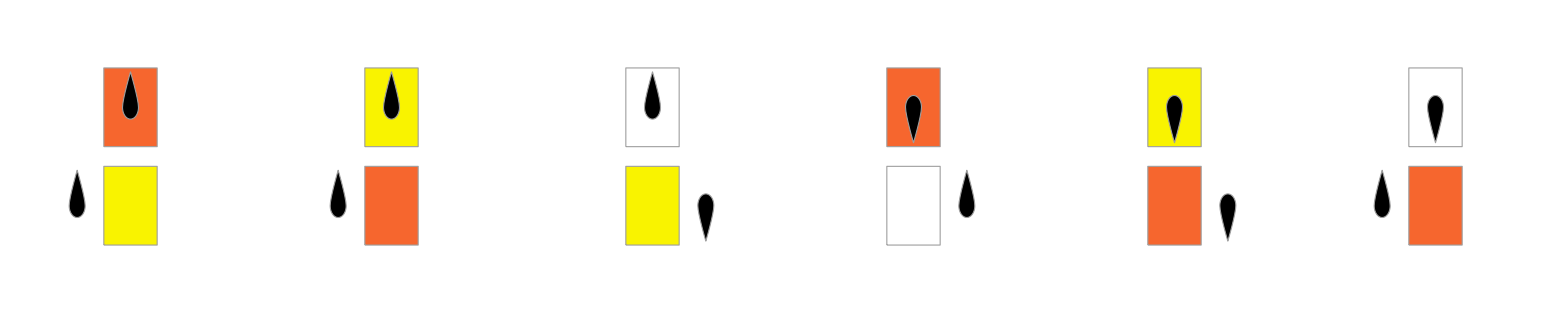

```mathematica
RulePlot[tM]
```

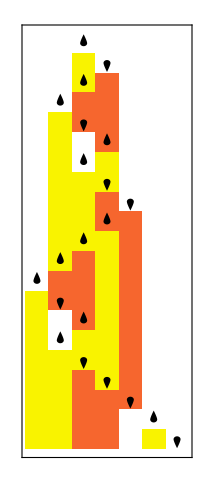

```mathematica
RulePlot[tM,{1,{{},0}},20]
```

```mathematica
tMRule=ResourceFunction["ComputationalSystemRules"][tM];
```

```mathematica
tmToCWTMRule=TMToCWTM[tMRule]
```

{{1,2}→{Fl[1,1],{Ml}},{1,1}→{Fl[1,2],{Ml}},{1,0}→{2,{1}},{1,L}→{2,{L,1}},{1,R}→{Fr[1],{Ml,R}},{2,2}→{1,{0}},{2,1}→{2,{2}},{2,0}→{Fl[1,2],{Ml}},{2,R}→{Fl[1,R],{Ml,2}},{2,L}→{Fl[1,2],{L,Ml}},{Fl[1,2],2}→{Fl[1,2],{2}},{Fl[1,2],1}→{Fl[1,1],{2}},{Fl[1,2],0}→{Fl[1,0],{2}},{Fl[1,2],L}→{Fl[1,L],{2}},{Fl[1,2],R}→{Fl[1,R],{2}},{Fl[1,2],Ml}→{Fl[1,1],{Ml}},{Fr[1],2}→{Fr[1],{2}},{Fr[1],Ml}→{2,{1}},{Fl[1,1],2}→{Fl[1,2],{1}},{Fl[1,1],1}→{Fl[1,1],{1}},{Fl[1,1],0}→{Fl[1,0],{1}},{Fl[1,1],L}→{Fl[1,L],{1}},{Fl[1,1],R}→{Fl[1,R],{1}},{Fl[1,1],Ml}→{Fl[1,2],{Ml}},{Fr[1],1}→{Fr[1],{1}},{Fr[1],Ml}→{2,{1}},{Fl[1,0],2}→{Fl[1,2],{0}},{Fl[1,0],1}→{Fl[1,1],{0}},{Fl[1,0],0}→{Fl[1,0],{0}},{Fl[1,0],L}→{Fl[1,L],{0}},{Fl[1,0],R}→{Fl[1,R],{0}},{Fl[1,0],Ml}→{2,{1}},{Fr[1],0}→{Fr[1],{0}},{Fr[1],Ml}→{2,{1}},{Fl[1,L],2}→{Fl[1,2],{L}},{Fl[1,L],1}→{Fl[1,1],{L}},{Fl[1,L],0}→{Fl[1,0],{L}},{Fl[1,L],L}→{Fl[1,L],{L}},{Fl[1,L],R}→{Fl[1,R],{L}},{Fl[1,L],Ml}→{2,{L,1}},{Fr[1],L}→{Fr[1],{L}},{Fr[1],Ml}→{2,{1}},{Fl[1,R],2}→{Fl[1,2],{R}},{Fl[1,R],1}→{Fl[1,1],{R}},{Fl[1,R],0}→{Fl[1,0],{R}},{Fl[1,R],L}→{Fl[1,L],{R}},{Fl[1,R],R}→{Fl[1,R],{R}},{Fl[1,R],Ml}→{Fr[1],{Ml,R}},{Fr[1],R}→{Fr[1],{R}},{Fr[1],Ml}→{2,{1}},{Fl[2,2],2}→{Fl[2,2],{2}},{Fl[2,2],1}→{Fl[2,1],{2}},{Fl[2,2],0}→{Fl[2,0],{2}},{Fl[2,2],L}→{Fl[2,L],{2}},{Fl[2,2],R}→{Fl[2,R],{2}},{Fl[2,2],Ml}→{1,{0}},{Fr[2],2}→{Fr[2],{2}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,1],2}→{Fl[2,2],{1}},{Fl[2,1],1}→{Fl[2,1],{1}},{Fl[2,1],0}→{Fl[2,0],{1}},{Fl[2,1],L}→{Fl[2,L],{1}},{Fl[2,1],R}→{Fl[2,R],{1}},{Fl[2,1],Ml}→{2,{2}},{Fr[2],1}→{Fr[2],{1}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,0],2}→{Fl[2,2],{0}},{Fl[2,0],1}→{Fl[2,1],{0}},{Fl[2,0],0}→{Fl[2,0],{0}},{Fl[2,0],L}→{Fl[2,L],{0}},{Fl[2,0],R}→{Fl[2,R],{0}},{Fl[2,0],Ml}→{Fl[1,2],{Ml}},{Fr[2],0}→{Fr[2],{0}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,R],2}→{Fl[2,2],{R}},{Fl[2,R],1}→{Fl[2,1],{R}},{Fl[2,R],0}→{Fl[2,0],{R}},{Fl[2,R],L}→{Fl[2,L],{R}},{Fl[2,R],R}→{Fl[2,R],{R}},{Fl[2,R],Ml}→{Fl[1,R],{Ml,2}},{Fr[2],R}→{Fr[2],{R}},{Fr[2],Ml}→{Fl[1,2],{Ml}},{Fl[2,L],2}→{Fl[2,2],{L}},{Fl[2,L],1}→{Fl[2,1],{L}},{Fl[2,L],0}→{Fl[2,0],{L}},{Fl[2,L],L}→{Fl[2,L],{L}},{Fl[2,L],R}→{Fl[2,R],{L}},{Fl[2,L],Ml}→{Fl[1,2],{L,Ml}},{Fr[2],L}→{Fr[2],{L}},{Fr[2],Ml}→{Fl[1,2],{Ml}}}

```mathematica
cWTM[tmToCWTMRule,TMToCWTMInit[{1,{0}}],50]//Column
```

{1,{0,R,L}}
{2,{R,L,1}}
{Fl[1,R],{L,1,Ml,2}}
{Fl[1,L],{1,Ml,2,R}}
{Fl[1,1],{Ml,2,R,L}}
{Fl[1,2],{2,R,L,Ml}}
{Fl[1,2],{R,L,Ml,2}}
{Fl[1,R],{L,Ml,2,2}}
{Fl[1,L],{Ml,2,2,R}}
{2,{2,2,R,L,1}}
{1,{2,R,L,1,0}}
{Fl[1,1],{R,L,1,0,Ml}}
{Fl[1,R],{L,1,0,Ml,1}}
{Fl[1,L],{1,0,Ml,1,R}}
{Fl[1,1],{0,Ml,1,R,L}}
{Fl[1,0],{Ml,1,R,L,1}}
{2,{1,R,L,1,1}}
{2,{R,L,1,1,2}}
{Fl[1,R],{L,1,1,2,Ml,2}}
{Fl[1,L],{1,1,2,Ml,2,R}}
{Fl[1,1],{1,2,Ml,2,R,L}}
{Fl[1,1],{2,Ml,2,R,L,1}}
{Fl[1,2],{Ml,2,R,L,1,1}}
{Fl[1,1],{2,R,L,1,1,Ml}}
{Fl[1,2],{R,L,1,1,Ml,1}}
{Fl[1,R],{L,1,1,Ml,1,2}}
{Fl[1,L],{1,1,Ml,1,2,R}}
{Fl[1,1],{1,Ml,1,2,R,L}}
{Fl[1,1],{Ml,1,2,R,L,1}}
{Fl[1,2],{1,2,R,L,1,Ml}}
{Fl[1,1],{2,R,L,1,Ml,2}}
{Fl[1,2],{R,L,1,Ml,2,1}}
{Fl[1,R],{L,1,Ml,2,1,2}}
{Fl[1,L],{1,Ml,2,1,2,R}}
{Fl[1,1],{Ml,2,1,2,R,L}}
{Fl[1,2],{2,1,2,R,L,Ml}}
{Fl[1,2],{1,2,R,L,Ml,2}}
{Fl[1,1],{2,R,L,Ml,2,2}}
{Fl[1,2],{R,L,Ml,2,2,1}}
{Fl[1,R],{L,Ml,2,2,1,2}}
{Fl[1,L],{Ml,2,2,1,2,R}}
{2,{2,2,1,2,R,L,1}}
{1,{2,1,2,R,L,1,0}}
{Fl[1,1],{1,2,R,L,1,0,Ml}}
{Fl[1,1],{2,R,L,1,0,Ml,1}}
{Fl[1,2],{R,L,1,0,Ml,1,1}}
{Fl[1,R],{L,1,0,Ml,1,1,2}}
{Fl[1,L],{1,0,Ml,1,1,2,R}}
{Fl[1,1],{0,Ml,1,1,2,R,L}}
{Fl[1,0],{Ml,1,1,2,R,L,1}}
{2,{1,1,2,R,L,1,1}}

```mathematica
cWTMRule={{1,0}->{2,{0,1}},{2,0}->{2,{2}},{3,0}->{1,{0}},{1,1}->{2,{0}},{2,1}->{3,{1}},{3,1}->{1,{0,0}},{1,2}->{3,{0}},{2,2}->{1,{2,2}},{3,2}->{2,{1}}};
```

```mathematica
cWTM[cWTMRule,{1,{0}},20]//Column
```

{1,{0}}
{2,{0,1}}
{2,{1,2}}
{3,{2,1}}
{2,{1,1}}
{3,{1,1}}
{1,{1,0,0}}
{2,{0,0,0}}
{2,{0,0,2}}
{2,{0,2,2}}
{2,{2,2,2}}
{1,{2,2,2,2}}
{3,{2,2,2,0}}
{2,{2,2,0,1}}
{1,{2,0,1,2,2}}
{3,{0,1,2,2,0}}
{1,{1,2,2,0,0}}
{2,{2,2,0,0,0}}
{1,{2,0,0,0,2,2}}
{3,{0,0,0,2,2,0}}
{1,{0,0,2,2,0,0}}

```mathematica
coloredToBinCWTMRule=ColoredToBinCWTM[cWTMRule]
```

{{Li[1,{{0}},{0}],0}→{Li[2,{{0,0},{0,1}},{}],{0}},{Li[1,{{0,0}},{0}],0}→{Li[2,{{0,0},{0,1}},{}],{0,0}},{Li[1,{{1,0}},{0}],0}→{Li[2,{{0,0},{0,1}},{}],{1,0}},{Li[2,{{0,0},{0,1}},{}],0}→{Li[2,{{0,1}},{0}],{0,0}},{Li[2,{{0,0},{0,1}},{}],1}→{Li[2,{{0,1}},{1}],{0,0}},{Li[2,{{0,1}},{0}],0}→{Li[2,{{1},{0}},{}],{0,1}},{Li[2,{{0}},{0}],0}→{Li[2,{{1},{0}},{}],{0}},{Li[2,{{1}},{0}],0}→{Li[2,{{1},{0}},{}],{1}},{Li[2,{{1},{0}},{}],0}→{Li[2,{{0}},{0}],{1}},{Li[2,{{1},{0}},{}],1}→{Li[2,{{0}},{1}],{1}},{Li[3,{{1}},{0}],0}→{Li[1,{{0},{0}},{}],{1}},{Li[3,{{0}},{0}],0}→{Li[1,{{0},{0}},{}],{0}},{Li[1,{{0},{0}},{}],0}→{Li[1,{{0}},{0}],{0}},{Li[1,{{0},{0}},{}],1}→{Li[1,{{0}},{1}],{0}},{Li[1,{{0}},{0}],1}→{Li[2,{{0},{0}},{}],{0}},{Li[1,{{0,0}},{0}],1}→{Li[2,{{0},{0}},{}],{0,0}},{Li[1,{{1,0}},{0}],1}→{Li[2,{{0},{0}},{}],{1,0}},{Li[2,{{0},{0}},{}],0}→{Li[2,{{0}},{0}],{0}},{Li[2,{{0},{0}},{}],1}→{Li[2,{{0}},{1}],{0}},{Li[2,{{0,1}},{0}],1}→{Li[3,{{0},{1}},{}],{0,1}},{Li[2,{{0}},{0}],1}→{Li[3,{{0},{1}},{}],{0}},{Li[2,{{1}},{0}],1}→{Li[3,{{0},{1}},{}],{1}},{Li[3,{{0},{1}},{}],0}→{Li[3,{{1}},{0}],{0}},{Li[3,{{0},{1}},{}],1}→{Li[3,{{1}},{1}],{0}},{Li[3,{{1}},{0}],1}→{Li[1,{{0,0},{0,0}},{}],{1}},{Li[3,{{0}},{0}],1}→{Li[1,{{0,0},{0,0}},{}],{0}},{Li[1,{{0,0},{0,0}},{}],0}→{Li[1,{{0,0}},{0}],{0,0}},{Li[1,{{0,0},{0,0}},{}],1}→{Li[1,{{0,0}},{1}],{0,0}},{Li[1,{{0}},{1}],0}→{Li[3,{{0},{0}},{}],{0}},{Li[1,{{0,0}},{1}],0}→{Li[3,{{0},{0}},{}],{0,0}},{Li[1,{{1,0}},{1}],0}→{Li[3,{{0},{0}},{}],{1,0}},{Li[3,{{0},{0}},{}],0}→{Li[3,{{0}},{0}],{0}},{Li[3,{{0},{0}},{}],1}→{Li[3,{{0}},{1}],{0}},{Li[2,{{0,1}},{1}],0}→{Li[1,{{1,0},{1,0}},{}],{0,1}},{Li[2,{{0}},{1}],0}→{Li[1,{{1,0},{1,0}},{}],{0}},{Li[2,{{1}},{1}],0}→{Li[1,{{1,0},{1,0}},{}],{1}},{Li[1,{{1,0},{1,0}},{}],0}→{Li[1,{{1,0}},{0}],{1,0}},{Li[1,{{1,0},{1,0}},{}],1}→{Li[1,{{1,0}},{1}],{1,0}},{Li[3,{{1}},{1}],0}→{Li[2,{{0},{1}},{}],{1}},{Li[3,{{0}},{1}],0}→{Li[2,{{0},{1}},{}],{0}},{Li[2,{{0},{1}},{}],0}→{Li[2,{{1}},{0}],{0}},{Li[2,{{0},{1}},{}],1}→{Li[2,{{1}},{1}],{0}}}

```mathematica
Grid[cWTM[coloredToBinCWTMRule,ColoredToBinCWTMInit[{1,{0}},cWTMRule],25],Alignment->Left]
```

Li[2,{{0,1}},{0}] | {0}
Li[2,{{1},{0}},{}] | {0,1}
Li[2,{{0}},{0}] | {1,1}
Li[3,{{0},{1}},{}] | {1,0}
Li[3,{{1}},{1}] | {0,0}
Li[2,{{0},{1}},{}] | {0,1}
Li[2,{{1}},{0}] | {1,0}
Li[3,{{0},{1}},{}] | {0,1}
Li[3,{{1}},{0}] | {1,0}
Li[1,{{0,0},{0,0}},{}] | {0,1}
Li[1,{{0,0}},{0}] | {1,0,0}
Li[2,{{0},{0}},{}] | {0,0,0,0}
Li[2,{{0}},{0}] | {0,0,0,0}
Li[2,{{1},{0}},{}] | {0,0,0,0}
Li[2,{{0}},{0}] | {0,0,0,1}
Li[2,{{1},{0}},{}] | {0,0,1,0}
Li[2,{{0}},{0}] | {0,1,0,1}
Li[2,{{1},{0}},{}] | {1,0,1,0}
Li[2,{{0}},{1}] | {0,1,0,1}
Li[1,{{1,0},{1,0}},{}] | {1,0,1,0}
Li[1,{{1,0}},{1}] | {0,1,0,1,0}
Li[3,{{0},{0}},{}] | {1,0,1,0,1,0}
Li[3,{{0}},{1}] | {0,1,0,1,0,0}
Li[2,{{0},{1}},{}] | {1,0,1,0,0,0}
Li[2,{{1}},{1}] | {0,1,0,0,0,0}
Li[1,{{1,0},{1,0}},{}] | {1,0,0,0,0,1}

```mathematica
cWTMBinRule={{0,0}->{1,{0}},{0,1}->{0,{0}},{1,0}->{0,{1,1}},{1,1}->{0,{1}}};
```

```mathematica
cWTM[cWTMBinRule,{1,{0}},20]//Column
```

{1,{0}}
{0,{1,1}}
{0,{1,0}}
{0,{0,0}}
{1,{0,0}}
{0,{0,1,1}}
{1,{1,1,0}}
{0,{1,0,1}}
{0,{0,1,0}}
{1,{1,0,0}}
{0,{0,0,1}}
{1,{0,1,0}}
{0,{1,0,1,1}}
{0,{0,1,1,0}}
{1,{1,1,0,0}}
{0,{1,0,0,1}}
{0,{0,0,1,0}}
{1,{0,1,0,0}}
{0,{1,0,0,1,1}}
{0,{0,0,1,1,0}}
{1,{0,1,1,0,0}}

```mathematica
cWTMToTagRule=CWTMToTag[cWTMBinRule]
```

{0→{},H_(1,0)→{H_(2,0),h_(2,0)},A_(1,0)→{A_(2,0),A_(2,0)},a_(1,0)→{C_(2,0),C_(2,0)},B_(1,0)→{B_(2,0),B_(2,0)},b_(1,0)→{D_(2,0),D_(2,0)},C_(1,0)→{C_(2,0),C_(2,0)},D_(1,0)→{D_(2,0),D_(2,0)},U_(1,0)→{U_(2,0),u_(2,0)},V_(1,0)→{V_(2,0),V_(2,0)},X_(1,0)→{X_(2,0),x_(2,0)},Y_(1,0)→{Y_(2,0),Y_(2,0)},H_(2,0)→{H_(3,0),$},h_(2,0)→{$,H_(3,0),$},A_(2,0)→{A_(3,0),A_(3,0)},B_(2,0)→{B_(3,0),B_(3,0)},C_(2,0)→{C_(3,0),C_(3,0)},D_(2,0)→{D_(3,0),D_(3,0)},U_(2,0)→{U_(3,0)},u_(2,0)→{V_(3,0)},X_(2,0)→{X_(3,0),X_(3,0)},x_(2,0)→{Y_(3,0),Y_(3,0)},V_(2,0)→{V_(3,0)},Y_(2,0)→{Y_(3,0),Y_(3,0)},H_(3,0)→{H_(4,0),h_(4,0)},A_(3,0)→{A_(4,0),a_(4,0)},B_(3,0)→{B_(4,0),b_(4,0)},C_(3,0)→{C_(4,0),c_(4,0)},D_(3,0)→{D_(4,0),d_(4,0)},U_(3,0)→{U_(4,0),u_(4,0),X_(4,0),x_(4,0)},V_(3,0)→{V_(4,0),v_(4,0),Y_(4,0),y_(4,0)},X_(3,0)→{X_(4,0),x_(4,0)},Y_(3,0)→{Y_(4,0),y_(4,0)},h_(4,0)→{},a_(4,0)→{$,P_(5,0),$},b_(4,0)→{$,Q_(5,0),$},c_(4,0)→{A_(5,0),$},d_(4,0)→{B_(5,0),$},u_(4,0)→{},v_(4,0)→{},x_(4,0)→{U_(5,0),x_(4,0)},y_(4,0)→{V_(5,0),y_(4,0)},P_(5,0)→{P_(6,0),$},Q_(5,0)→{Q_(6,0)},A_(5,0)→{A_(6,0),a_(6,0)},B_(5,0)→{B_(6,0),b_(6,0)},U_(5,0)→{U_(6,0),u_(6,0)},V_(5,0)→{V_(6,0),v_(6,0)},H_(4,0)→{H_(1,0),$},A_(4,0)→{A_(1,0),a_(1,0),0},B_(4,0)→{B_(1,0),b_(1,0),0},C_(4,0)→{C_(1,0),C_(1,0)},D_(4,0)→{D_(1,0),D_(1,0)},U_(4,0)→{U_(1,0),U_(1,0)},V_(4,0)→{V_(1,0),V_(1,0)},X_(4,0)→{X_(1,0),X_(1,0)},Y_(4,0)→{Y_(1,0),Y_(1,0)},A_(6,0)→{A_(3,1),A_(3,1)},B_(6,0)→{B_(3,1),B_(3,1)},V_(6,0)→{U_(3,1)},U_(6,0)→{U_(3,1),U_(3,1)},a_(6,0)→{A_(3,0),A_(3,0)},b_(6,0)→{B_(3,0),B_(3,0)},v_(6,0)→{U_(3,0)},u_(6,0)→{U_(3,0),U_(3,0)},P_(6,0)→{A_(6,0),a_(6,0),H_(3,1),$},Q_(6,0)→{A_(6,0),a_(6,0),$,H_(3,0),$},H_(1,1)→{H_(2,1),h_(2,1)},A_(1,1)→{A_(2,1),A_(2,1)},a_(1,1)→{C_(2,1),C_(2,1)},B_(1,1)→{B_(2,1),B_(2,1)},b_(1,1)→{D_(2,1),D_(2,1)},C_(1,1)→{C_(2,1),C_(2,1)},D_(1,1)→{D_(2,1),D_(2,1)},U_(1,1)→{U_(2,1),u_(2,1)},V_(1,1)→{V_(2,1),V_(2,1)},X_(1,1)→{X_(2,1),x_(2,1)},Y_(1,1)→{Y_(2,1),Y_(2,1)},H_(2,1)→{H_(3,1),$},h_(2,1)→{$,H_(3,1),$},A_(2,1)→{A_(3,1),A_(3,1)},B_(2,1)→{B_(3,1),B_(3,1)},C_(2,1)→{C_(3,1),C_(3,1)},D_(2,1)→{D_(3,1),D_(3,1)},U_(2,1)→{U_(3,1)},u_(2,1)→{V_(3,1)},X_(2,1)→{X_(3,1),X_(3,1)},x_(2,1)→{Y_(3,1),Y_(3,1)},V_(2,1)→{V_(3,1)},Y_(2,1)→{Y_(3,1),Y_(3,1)},H_(3,1)→{H_(4,1),h_(4,1)},A_(3,1)→{A_(4,1),a_(4,1)},B_(3,1)→{B_(4,1),b_(4,1)},C_(3,1)→{C_(4,1),c_(4,1)},D_(3,1)→{D_(4,1),d_(4,1)},U_(3,1)→{U_(4,1),u_(4,1),X_(4,1),x_(4,1)},V_(3,1)→{V_(4,1),v_(4,1),Y_(4,1),y_(4,1)},X_(3,1)→{X_(4,1),x_(4,1)},Y_(3,1)→{Y_(4,1),y_(4,1)},h_(4,1)→{},a_(4,1)→{$,P_(5,1),$},b_(4,1)→{$,Q_(5,1),$},c_(4,1)→{A_(5,1),$},d_(4,1)→{B_(5,1),$},u_(4,1)→{},v_(4,1)→{},x_(4,1)→{U_(5,1),x_(4,1)},y_(4,1)→{V_(5,1),y_(4,1)},P_(5,1)→{P_(6,1),$},Q_(5,1)→{Q_(6,1)},A_(5,1)→{A_(6,1),a_(6,1)},B_(5,1)→{B_(6,1),b_(6,1)},U_(5,1)→{U_(6,1),u_(6,1)},V_(5,1)→{V_(6,1),v_(6,1)},H_(4,1)→{H_(1,1),$},A_(4,1)→{A_(1,1),a_(1,1),0},B_(4,1)→{B_(1,1),b_(1,1),0},C_(4,1)→{C_(1,1),C_(1,1)},D_(4,1)→{D_(1,1),D_(1,1)},U_(4,1)→{U_(1,1),U_(1,1)},V_(4,1)→{V_(1,1),V_(1,1)},X_(4,1)→{X_(1,1),X_(1,1)},Y_(4,1)→{Y_(1,1),Y_(1,1)},A_(6,1)→{A_(3,0),A_(3,0)},B_(6,1)→{B_(3,0),B_(3,0)},V_(6,1)→{U_(3,0)},U_(6,1)→{U_(3,0),U_(3,0)},a_(6,1)→{A_(3,0),A_(3,0)},b_(6,1)→{B_(3,0),B_(3,0)},v_(6,1)→{U_(3,0)},u_(6,1)→{U_(3,0),U_(3,0)},P_(6,1)→{B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$},Q_(6,1)→{B_(6,1),b_(6,1),$,H_(3,0),$}}

```mathematica
ResourceFunction["TagSystem"][{2,Replace[(x_->y_):>{x,_}->y]/@cWTMToTagRule},CWTMToTagInit[{1,{0}}],50]//Column
```

{H_(2,1),h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1),U_(2,1),u_(2,1)}
{A_(2,1),A_(2,1),U_(2,1),u_(2,1),U_(2,1),u_(2,1),H_(3,1),$}
{U_(2,1),u_(2,1),U_(2,1),u_(2,1),H_(3,1),$,A_(3,1),A_(3,1)}
{U_(2,1),u_(2,1),H_(3,1),$,A_(3,1),A_(3,1),U_(3,1)}
{H_(3,1),$,A_(3,1),A_(3,1),U_(3,1),U_(3,1)}
{A_(3,1),A_(3,1),U_(3,1),U_(3,1),H_(4,1),h_(4,1)}
{U_(3,1),U_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1)}
{H_(4,1),h_(4,1),A_(4,1),a_(4,1),U_(4,1),u_(4,1),X_(4,1),x_(4,1)}
{A_(4,1),a_(4,1),U_(4,1),u_(4,1),X_(4,1),x_(4,1),H_(1,1),$}
{U_(4,1),u_(4,1),X_(4,1),x_(4,1),H_(1,1),$,A_(1,1),a_(1,1),0}
{X_(4,1),x_(4,1),H_(1,1),$,A_(1,1),a_(1,1),0,U_(1,1),U_(1,1)}
{H_(1,1),$,A_(1,1),a_(1,1),0,U_(1,1),U_(1,1),X_(1,1),X_(1,1)}
{A_(1,1),a_(1,1),0,U_(1,1),U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1)}
{0,U_(1,1),U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1)}
{U_(1,1),X_(1,1),X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1)}
{X_(1,1),H_(2,1),h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1)}
{h_(2,1),A_(2,1),A_(2,1),U_(2,1),u_(2,1),X_(2,1),x_(2,1)}
{A_(2,1),U_(2,1),u_(2,1),X_(2,1),x_(2,1),$,H_(3,1),$}
{u_(2,1),X_(2,1),x_(2,1),$,H_(3,1),$,A_(3,1),A_(3,1)}
{x_(2,1),$,H_(3,1),$,A_(3,1),A_(3,1),V_(3,1)}
{H_(3,1),$,A_(3,1),A_(3,1),V_(3,1),Y_(3,1),Y_(3,1)}
{A_(3,1),A_(3,1),V_(3,1),Y_(3,1),Y_(3,1),H_(4,1),h_(4,1)}
{V_(3,1),Y_(3,1),Y_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1)}
{Y_(3,1),H_(4,1),h_(4,1),A_(4,1),a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1)}
{h_(4,1),A_(4,1),a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1)}
{a_(4,1),V_(4,1),v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1)}
{v_(4,1),Y_(4,1),y_(4,1),Y_(4,1),y_(4,1),$,P_(5,1),$}
{y_(4,1),Y_(4,1),y_(4,1),$,P_(5,1),$}
{y_(4,1),$,P_(5,1),$,V_(5,1),y_(4,1)}
{P_(5,1),$,V_(5,1),y_(4,1),V_(5,1),y_(4,1)}
{V_(5,1),y_(4,1),V_(5,1),y_(4,1),P_(6,1),$}
{V_(5,1),y_(4,1),P_(6,1),$,V_(6,1),v_(6,1)}
{P_(6,1),$,V_(6,1),v_(6,1),V_(6,1),v_(6,1)}
{V_(6,1),v_(6,1),V_(6,1),v_(6,1),B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$}
{V_(6,1),v_(6,1),B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$,U_(3,0)}
{B_(6,1),b_(6,1),B_(6,1),b_(6,1),H_(3,0),$,U_(3,0),U_(3,0)}
{B_(6,1),b_(6,1),H_(3,0),$,U_(3,0),U_(3,0),B_(3,0),B_(3,0)}
{H_(3,0),$,U_(3,0),U_(3,0),B_(3,0),B_(3,0),B_(3,0),B_(3,0)}
{U_(3,0),U_(3,0),B_(3,0),B_(3,0),B_(3,0),B_(3,0),H_(4,0),h_(4,0)}
{B_(3,0),B_(3,0),B_(3,0),B_(3,0),H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0)}
{B_(3,0),B_(3,0),H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0)}
{H_(4,0),h_(4,0),U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0)}
{U_(4,0),u_(4,0),X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$}
{X_(4,0),x_(4,0),B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0)}
{B_(4,0),b_(4,0),B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0)}
{B_(4,0),b_(4,0),H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0}
{H_(1,0),$,U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0}
{U_(1,0),U_(1,0),X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0)}
{X_(1,0),X_(1,0),B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0)}
{B_(1,0),b_(1,0),0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0),X_(2,0),x_(2,0)}
{0,B_(1,0),b_(1,0),0,H_(2,0),h_(2,0),U_(2,0),u_(2,0),X_(2,0),x_(2,0),B_(2,0),B_(2,0)}

```mathematica
tagRule={2->{0,2,1,2},1->{0},0->{2,1}};
```

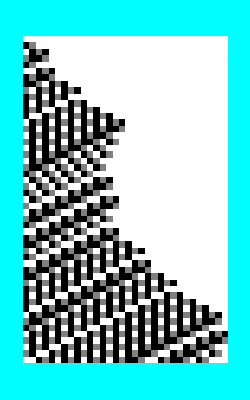

```mathematica
ArrayPlot[ResourceFunction["TagSystem"][{2,Replace[(x_->y_):>{x,_}->y]/@tagRule},{0,0},50],Background->Cyan]
```

```mathematica
tag1ToCTRule=Tag1ToCT[{2,tagRule}]
```

{{0,0,1,0,1,0},{1,0,0},{1,0,0,0,0,1,0,1,0,0,0,1},{},{},{}}

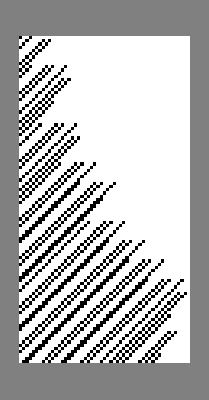

```mathematica
ArrayPlot[ResourceFunction["CyclicTagSystem"][tag1ToCTRule,Tag1ToCTInit[{0,0},tagRule],100],Background->Gray]
```